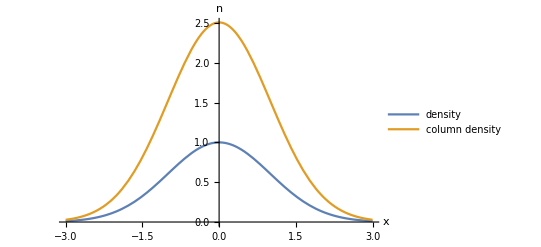

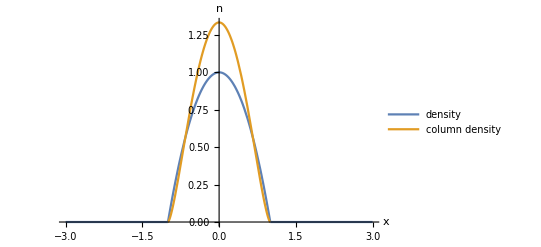

```mathematica
Clear [n0,sx,sy,sz,R0];
nGauss[x_,y_,z_]:= n0*Exp[-1/2*((x/sx)^2+(y/sy)^2+(z/sz)^2)];
colnGauss[x_,y_]:= n0*Exp[-1/2*((x/sx)^2+(y/sy)^2)]*Sqrt[Pi*2*sz];

nTF[x_,y_,z_]:= n0*(1-(x^2+y^2+z^2)/R0^2);
colnTF[x_,y_]:= n0/R0^2*4/3*(R0^2-(x^2+y^2))^(3/2);

n0=1;
sx = 1;sy=1;sz = 1;
R0 =1; 

Plot[{nGauss[x,0,0],colnGauss[x,0]},{x,-3,3},PlotLegends->{"density","column density"},AxesLabel->{"x","n"}]
Plot[{Piecewise[{{0*x,x<-1},{nTF[x,0,0],-1<x<1},{0*x,x>1}}],colnTF[x,0]},{x,-3,3},PlotLegends->{"density","column density"},AxesLabel->{"x","n"}]
```

```mathematica
Clear [n0,sx,sy,sz,R0];
Integrate[nGauss[x,y,z],{x,-Infinity,Infinity},{y,-Infinity,Infinity},{z,-Infinity,Infinity}];
```